```mathematica
(*Subscript[f, column]*)
Nn= 4;
Manipulate[Grid@Table[Subscript[c, n] e^(i n Subscript[x, k]),{n,0,nmax},{k,0,kmax}],{nmax,0,Nn-1},{kmax,0,Nn-1}]
```

```mathematica
(*Subscript[c, row]*)
Manipulate[Grid@Join[
Table[Subscript[f, k] e^(-i n Subscript[x, k]),{n,0,nmax},{k,0,kmax}],
Table[{0,1,4,9}[[k+1]]Exp[-(ⅈ 2π n k)/4],{n,0,nmax},{k,0,kmax}]
],{nmax,0,Nn-1},{kmax,0,Nn-1}]
(*Manipulate[Grid@Table[{0,1,4,9}[[k+1]]Exp[-(ⅈ 2π n k)/4],{n,0,nmax},{k,0,kmax}],{nmax,0,3},{kmax,0,3}]*)
```

```mathematica
dft[f_List]:= With[{t=Length[f]},Column@Table[Total@Table[f[[k+1]]Exp[-(ⅈ 2π n k)/t],{k,0,t-1}],{n,0,t-1}]]
dft[{0,1,4,9}]
```

14
-4+8 ⅈ
-6
-4-8 ⅈ

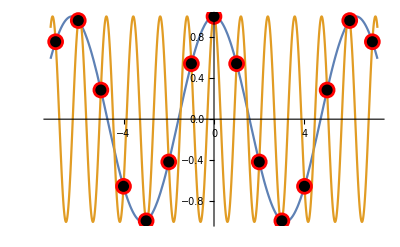

```mathematica
points1 = Join[{PointSize[0.03]},Table[{Red,Point[{i,Cos[i]}]},{i,-7,7}]];
points2 = Join[{PointSize[0.02]},Table[{Black,Point[{i,Cos[(2π-1)i]}]},{i,-7,7}]];
Plot[{Cos[t],Cos[(2π-1)t]},{t,-2.3π,2.3π},Epilog->Join[points1,points2]]
```

```mathematica
2Fourier[{0,1,4,9}]
```

{14.+0. ⅈ,-4.-8. ⅈ,-6.+0. ⅈ,-4.+8. ⅈ}

```mathematica
fft[{x_,y_},n_] := x+y Exp[-ⅈ π n ]
fft[f_List,n_]:=fft[Downsample[f,2,1],n]+Exp[-(ⅈ 2π n)/Length[f]]fft[Downsample[f,2,2],n]
fft[f_List]:= Table[fft[f,n]//N,{n,0,Length[f]-1}]
Column@fft[{0,1,4,9}]
fft[{1,0},0]
fft[{4,9},0]
```

14.
-4.+8. ⅈ
-6.
-4.-8. ⅈ

1

13